# H(Ω, div) Basis Functions

## Building traditional HDiv functions

## Vector Field at Vertices (Quadrilateral Element)

```mathematica
VectorField[]:= {{0, -1},
				 {0, -1},
				 {1, 0},
				 {1, 0},
				 {0, 1},
				 {0, 1},
				 {-1, 0},
				 {-1, 0},
				 {1, 0},
				 {0, 1},
				 {-1, 0},
				 {0, -1}}
```

## H1 - Conforming Basis Functions

```mathematica
ClearAll[H1Basis]
H1Basis[n_]:= Block[{phivar,  dphivar, nshape, subst, chebx,x,orders,orderscsi,orderseta},
	chebx=Table[ChebyshevT[i,x],{i,0,n-2}];
	nshape = (n+1)(n+1);
	orders=Table[{{1,1}},{4}];
	
	phivar = Table[{},{9}];
		
	phivar[[1]] = {1/4(1-csi)(1-eta)};
	phivar[[2]] = {1/4(1+csi)(1-eta)};
	phivar[[3]] = {1/4(1+csi)(1+eta)};
	phivar[[4]] = {1/4(1-csi)(1+eta)}; 
	If[n==1,
		dphivar=Grad[Flatten[phivar],{csi,eta}];
		Return[{phivar,dphivar,orders}]
	];
	
	phivar[[5]] = 4 phivar[[1,1]](phivar[[2,1]] + phivar[[3,1]])(chebx/.x->csi)//Simplify;
	AppendTo[orders,Table[{i,1},{i,2,n}]];
	phivar[[6]] = 4 phivar[[2,1]](phivar[[3,1]] + phivar[[4,1]])(chebx/.x->eta)//Simplify;
	AppendTo[orders,Table[{1,i},{i,2,n}]];
	phivar[[7]] = 4 phivar[[3,1]](phivar[[4,1]] + phivar[[1,1]])(chebx/.x->csi)//Simplify;
	AppendTo[orders,Table[{i,1},{i,2,n}]];
	phivar[[8]] = 4 phivar[[4,1]](phivar[[1,1]] + phivar[[2,1]])(chebx/.x->eta)//Simplify;
	AppendTo[orders,Table[{1,i},{i,2,n}]];
	
	phivar[[9]] = 16 phivar[[1,1]]phivar[[3,1]]Flatten[Outer[Times,chebx/.x->csi,chebx/.x->eta]]//Simplify;
	AppendTo[orders,Flatten[Table[{i,j},{i,2,n},{j,2,n}],1]];
	dphivar=Grad[Flatten[phivar],{csi,eta}]//Simplify;
		
	{phivar, dphivar,orders}
]
```

## H(Ω, div) Basis Functions

```mathematica
HDivBasis[n_]:=Block[{v, phidiv, i, j,aux,phi,dphi,orders},
	{phi,dphi,orders}=H1Basis[n+1];
	v = VectorField[];
	
	phidiv=Table[{},{5}];
	(*Print["#phidiv ",8+4(n-1)+4n+2(n-1)n];*)
	aux = {0,1,1,2,3,2,0,3,4,5,6,7};
	
	For[i=1, i<=4, i++,
		AppendTo[phidiv[[i]],phi[[aux[[2i-1]]+1,1]] v[[2i-1]]];
		AppendTo[phidiv[[i]],phi[[aux[[2i]]+1,1]] v[[2i]]];
		For[j=1,j<n,j++,
			AppendTo[phidiv[[i]],phi[[5]][[j]]v[[2i-1]]];
		];
	];
	For[i=5,i<=8,i++,
		For[j=1,j<=n,j++,
			AppendTo[phidiv[[5]],phi[[i]][[j]]v[[i+4]]];
		];
	];
	For[i=1,i<=Length[phi[[9]]],i++,
		If[orders[[9,i,1]]<=n+1 && orders[[9,i,2]]<=n,AppendTo[phidiv[[5]],phi[[9]][[i]]{1,0}]];
		If[orders[[9,i,1]]<=n && orders[[9,i,2]]<=n+1,AppendTo[phidiv[[5]],phi[[9]][[i]]{0,1}]];
	];
	
	phidiv
]
```

## H1-Conforming Transformation

```mathematica
(*H1-conforming transformation*)
Te[X_, phi_, dphi_]:= Block[{x, gradx},
x={X[[;;,1]].phi[[1;;4,1]],X[[;;,2]].phi[[1;;4,1]]};
gradx={X[[;;,1]].dphi[[1;;4]],X[[;;,2]].dphi[[1;;4]]}//Transpose;
	Simplify[{x, gradx}]
]
```

## Jacobian

```mathematica
(*Jacobian and its determinant*)
Jacob[gradx_]:=Block[{J, detJac},
	
	J = gradx;
	
	detJac = Det[J];
	
	{J, detJac}
]
```

## Piola Transformation

```mathematica
(*Hdiv transformation*)
PiolaTransf[J_, detJac_, phiHdiv_]:= Simplify[Transpose[J.Transpose[phiHdiv]]/detJac]
```

## Printing Results

```mathematica
PrintResults[phi_,orders_, dphi_, phiHdiv_, J_, detJac_, phit_]:=Block[{Null},
	Print["--- H1-Conforming Basis Functions ---"];
	Table[{Print[phi[[i]]//MatrixForm],Print[orders[[i]]]},{i,9}];
		
	Print["--- Derivative H1-Conforming Basis Functions ---"];
	Print[dphi//MatrixForm];
		
	Print["--- H(Ω, div) Basis Functions ---"];
	Table[Print[phiHdiv[[i]]//MatrixForm],{i,5}];
		
	Print["--- Jacobian ---"];
	Print[J//MatrixForm];
		
	Print["--- Jacobian Determinant ---"];
	Print[detJac];
		
	Print["--- Piola Transformation Te: Ω_ -> Ωhdiv ---"];
	Print[phit//MatrixForm];
]
```

2

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{0.,-1.5746},{0.,-0.2},{0.,-0.709839},{0.2,0.},{0.0254033,0.},{0.709839,0.},{0.,0.2},{0.,0.0254033},{0.,0.709839},{-1.5746,0.},{-0.2,0.},{-0.709839,0.},{0.709839,0.},{-0.549839,0.},{0.,0.0901613},{0.,-0.0698387},{-0.0901613,0.},{0.0698387,0.},{0.,-0.709839},{0.,0.549839},{0.32,0.},{0.,0.32},{0.,-0.247871},{-0.247871,0.}}

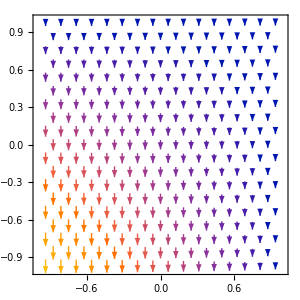
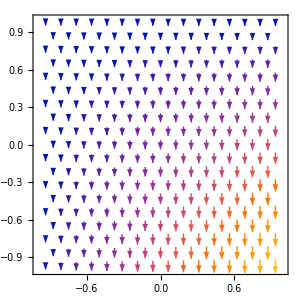
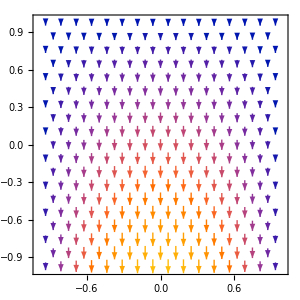
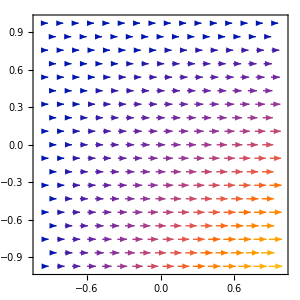
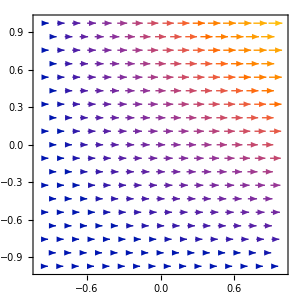
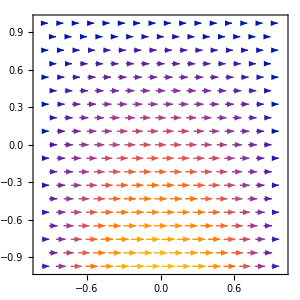
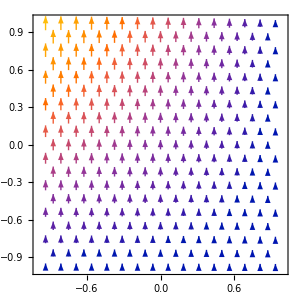
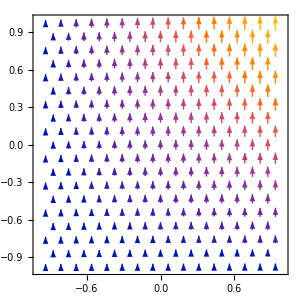

--- H1-Conforming Basis Functions ---

(1/4 (1-csi) (1-eta))

{{1,1}}

(1/4 (1+csi) (1-eta))

{{1,1}}

(1/4 (1+csi) (1+eta))

{{1,1}}

(1/4 (1-csi) (1+eta))

{{1,1}}

(1/2 (-1+csi) (1+csi) (-1+eta)
1/2 (-1+csi) csi (1+csi) (-1+eta))

{{2,1},{3,1}}

(-1/2 (1+csi) (-1+eta) (1+eta)
-1/2 (1+csi) (-1+eta) eta (1+eta))

{{1,2},{1,3}}

(-1/2 (-1+csi) (1+csi) (1+eta)
-1/2 (-1+csi) csi (1+csi) (1+eta))

{{2,1},{3,1}}

(1/2 (-1+csi) (-1+eta) (1+eta)
1/2 (-1+csi) (-1+eta) eta (1+eta))

{{1,2},{1,3}}

((-1+csi) (1+csi) (-1+eta) (1+eta)
(-1+csi) (1+csi) (-1+eta) eta (1+eta)
(-1+csi) csi (1+csi) (-1+eta) (1+eta)
(-1+csi) csi (1+csi) (-1+eta) eta (1+eta))

{{2,2},{2,3},{3,2},{3,3}}

--- Derivative H1-Conforming Basis Functions ---

(1/4 (-1+eta) | 1/4 (-1+csi)
(1-eta)/4 | 1/4 (-1-csi)
(1+eta)/4 | (1+csi)/4
1/4 (-1-eta) | (1-csi)/4
csi (-1+eta) | 1/2 (-1+csi) (1+csi)
1/2 (-1+3 csi^2) (-1+eta) | 1/2 (-1+csi) csi (1+csi)
-1/2 (-1+eta) (1+eta) | -((1+csi) eta)
-1/2 (-1+eta) eta (1+eta) | -1/2 (1+csi) (-1+3 eta^2)
-csi (1+eta) | -1/2 (-1+csi) (1+csi)
-1/2 (-1+3 csi^2) (1+eta) | -1/2 (-1+csi) csi (1+csi)
1/2 (-1+eta) (1+eta) | (-1+csi) eta
1/2 (-1+eta) eta (1+eta) | 1/2 (-1+csi) (-1+3 eta^2)
2 csi (-1+eta^2) | 2 (-1+csi^2) eta
2 csi eta (-1+eta^2) | (-1+csi^2) (-1+3 eta^2)
(-1+3 csi^2) (-1+eta^2) | 2 csi (-1+csi^2) eta
(-1+3 csi^2) eta (-1+eta^2) | csi (-1+csi^2) (-1+3 eta^2))

--- H(Ω, div) Basis Functions ---

(0 | -0.787298
0 | -0.1
0 | -0.354919)

(0.1 | 0
0.0127017 | 0
0.354919 | 0)

(0 | 0.1
0 | 0.0127017
0 | 0.354919)

(-0.787298 | 0
-0.1 | 0
-0.354919 | 0)

(0.354919 | 0
-0.274919 | 0
0 | 0.0450807
0 | -0.0349193
-0.0450807 | 0
0.0349193 | 0
0 | -0.354919
0 | 0.274919
0.16 | 0
0 | 0.16
0 | -0.123935
-0.123935 | 0)

--- Jacobian ---

(1/2 | 0
0 | 1/2)

--- Jacobian Determinant ---

1/4

--- Piola Transformation Te: Ω_ -> Ωhdiv ---

(0. | -1.5746
0. | -0.2
0. | -0.709839
0.2 | 0.
0.0254033 | 0.
0.709839 | 0.
0. | 0.2
0. | 0.0254033
0. | 0.709839
-1.5746 | 0.
-0.2 | 0.
-0.709839 | 0.
0.709839 | 0.
-0.549839 | 0.
0. | 0.0901613
0. | -0.0698387
-0.0901613 | 0.
0.0698387 | 0.
0. | -0.709839
0. | 0.549839
0.32 | 0.
0. | 0.32
0. | -0.247871
-0.247871 | 0.)

```mathematica
CSI1 = ETA1 = -0.7745966692414834;
subst = {csi->CSI1,eta->ETA1};
n=2
{phivar, dphivar,orders} = H1Basis[n+1];
Table[Plot3D[phivar[[i,1]],{csi,-1,1},{eta,-1,1}],{i,9}]


phidiv = HDivBasis[n]/.subst;
phidivgr = Flatten[HDivBasis[n],1];

(*Setting a random element coordinate*)
X = {{0,0}, {1,0}, {1,1}, {0,1}};

(*Transforming master element into deformed element*)
{x, gradx} = Te[X, phivar, dphivar];

(*Calculating jacobian matrix and its determinant*)
{J, detJac} = Jacob[gradx];

(*Applying Piola transformation in Hdiv vector functions*)
phit = PiolaTransf[J, detJac, Flatten[phidiv,1]]/.subst

Table[VectorPlot[phidivgr[[i]],{csi,-1,1},{eta,-1,1},VectorScaling->Automatic, ImageSize->300], {i,12}]
PrintResults[phivar, orders, dphivar, phidiv, J, detJac, phit];
```

## Testing traditional HDiv function

## The div(Hdiv) functions can be represented by L2 functions

```mathematica
n=2
L2Funcs=H1Basis[n];
HDivFuncs=Flatten[HDivBasis[n],1];
L2=L2Funcs[[1]]//Flatten;
div=Div[HDivFuncs,{csi,eta}]//Simplify;
allfunc=Join[L2,div];
L2Mat=Parallelize[Table[Quiet[Integrate[allfunc[[i]]allfunc[[j]],{csi,-1,1},{eta,-1,1}]],{i,1,Length[allfunc]},{j,1,Length[allfunc]}]];
L2Mat//MatrixForm;
nL2=Length[L2];
Res=L2Mat[[nL2+1;;,nL2+1;;]]-L2Mat[[nL2+1;;,1;;nL2]].LinearSolve[L2Mat[[1;;nL2,1;;nL2]],L2Mat[[1;;nL2,nL2+1;;]]];
(*Chop[Res]//MatrixForm*)
Norm[Res]
```

## The rank of the div basis has be equal to the number of L2 functions

```mathematica
MatrixRank[L2Mat[[nL2+1;;,nL2+1;;]]]
Length[L2]
```

## All monomials whose divergence belongs to the L2 space need to be represented

```mathematica
AllPolx=Flatten[Table[{csi^i eta^j,0},{i,0,n+1},{j,0,n}],1];
AllPoly=Flatten[Table[{0,csi^i eta^j},{i,0,n},{j,0,n+1}],1];
AllPolxy=Join[AllPolx,AllPoly];
npoly=Length[AllPolxy]
nhdiv=Length[HDivFuncs]
allfunc=Join[AllPolxy,HDivFuncs];
L2Mat=Parallelize[Table[Quiet[Integrate[allfunc[[i]].allfunc[[j]],{csi,-1,1},{eta,-1,1}]],{i,1,Length[allfunc]},{j,1,Length[allfunc]}]];
L2Mat//MatrixForm;
nL2=Length[AllPolxy];
Res=L2Mat[[nL2+1;;,nL2+1;;]]-L2Mat[[nL2+1;;,1;;nL2]].LinearSolve[L2Mat[[1;;nL2,1;;nL2]],L2Mat[[1;;nL2,nL2+1;;]]];
(*Chop[Res]//MatrixForm*)
Norm[Res]
```

## HDiv functions with optimized border functions

## HDiv border functions

```mathematica
HDivBorderBasis[n_]:=Block[{v, phidiv, i, j,aux,phi,dphi,orders},
	{phi,dphi,orders}=H1Basis[n+1];
	v = VectorField[];
	
	phidiv=Table[{},{5}];
	(*Print["#phidiv ",8+4(n-1)+4n+2(n-1)n];*)
	aux = {0,1,1,2,3,2,0,3,4,5,6,7};
	
	For[i=1, i<=4, i++,
		AppendTo[phidiv[[i]],phi[[aux[[2i-1]]+1,1]] v[[2i-1]]+phi[[aux[[2i]]+1,1]] v[[2i]]];
		For[j=1,j<=n,j++,
			AppendTo[phidiv[[i]],{-D[phi[[4+i]][[j]],eta],D[phi[[5]][[j]],csi]}];
		];
	];
	For[i=5,i<=8,i++,
		For[j=1,j<=n,j++,
			AppendTo[phidiv[[5]],phi[[i]][[j]]v[[i+4]]];
		];
	];
	For[i=1,i<=Length[phi[[9]]],i++,
		If[orders[[9,i,1]]<=n+1 && orders[[9,i,2]]<=n,AppendTo[phidiv[[5]],phi[[9]][[i]]{1,0}]];
		If[orders[[9,i,1]]<=n && orders[[9,i,2]]<=n+1,AppendTo[phidiv[[5]],phi[[9]][[i]]{0,1}]];
	];
	
	phidiv
]
```

## Testing HDiv function with optimized border

## The div(Hdiv) functions can be represented by L2 functions

```mathematica
n=2
L2Funcs=H1Basis[n];
HDivFuncs=Flatten[HDivBorderBasis[n],1];
L2=L2Funcs[[1]]//Flatten;
div=Div[HDivFuncs,{csi,eta}]//Simplify;
allfunc=Join[L2,div];
L2Mat=Parallelize[Table[Quiet[Integrate[allfunc[[i]]allfunc[[j]],{csi,-1,1},{eta,-1,1}]],{i,1,Length[allfunc]},{j,1,Length[allfunc]}]];
L2Mat//MatrixForm;
nL2=Length[L2];
Res=L2Mat[[nL2+1;;,nL2+1;;]]-L2Mat[[nL2+1;;,1;;nL2]].LinearSolve[L2Mat[[1;;nL2,1;;nL2]],L2Mat[[1;;nL2,nL2+1;;]]];
(*Chop[Res]//MatrixForm*)
Norm[Res]
```

## The rank of the div basis has be equal to the number of L2 functions

```mathematica
MatrixRank[L2Mat[[nL2+1;;,nL2+1;;]]]
Length[L2]
```

## All monomials whose divergence belongs to the L2 space need to be represented

```mathematica
AllPolx=Flatten[Table[{csi^i eta^j,0},{i,0,n+1},{j,0,n}],1];
AllPoly=Flatten[Table[{0,csi^i eta^j},{i,0,n},{j,0,n+1}],1];
AllPolxy=Join[AllPolx,AllPoly];
npoly=Length[AllPolxy]
nhdiv=Length[HDivFuncs]
allfunc=Join[AllPolxy,HDivFuncs];
L2Mat=Parallelize[Table[Quiet[Integrate[allfunc[[i]].allfunc[[j]],{csi,-1,1},{eta,-1,1}]],{i,1,Length[allfunc]},{j,1,Length[allfunc]}]];
L2Mat//MatrixForm;
nL2=Length[AllPolxy];
Res=L2Mat[[nL2+1;;,nL2+1;;]]-L2Mat[[nL2+1;;,1;;nL2]].LinearSolve[L2Mat[[1;;nL2,1;;nL2]],L2Mat[[1;;nL2,nL2+1;;]]];
(*Chop[Res]//MatrixForm*)
Norm[Res]
```

## HDiv Functions with separated divergence free and nonsingular div

```mathematica
HDivOptimizedBasis[n_]:=Block[{v, phidiv, i, j,aux,phi,dphi,orders},
	{phi,dphi,orders}=H1Basis[n+1];
	v = VectorField[];
	
	phidiv=Table[{},{10}];
	(*Print["#phidiv ",8+4(n-1)+4n+2(n-1)n];*)
	aux = {0,1,1,2,3,2,0,3,4,5,6,7};
	
	For[i=1, i<=4, i++,
		AppendTo[phidiv[[2i-1]],phi[[aux[[2i-1]]+1,1]] v[[2i-1]]+phi[[aux[[2i]]+1,1]] v[[2i]]];
		For[j=1,j<=n,j++,
			AppendTo[phidiv[[2i]],{-D[phi[[i+4]][[j]],eta],D[phi[[i+4]][[j]],csi]}];
		];
	];
	For[i=5,i<=7,i++,
		For[j=1,j<=n,j++,
			AppendTo[phidiv[[9]],phi[[i]][[j]]v[[i+4]]];
		];
	];
	For[i=1,i<=Length[phi[[9]]],i++,
		If[orders[[9,i,1]]<=n+1 && orders[[9,i,2]]<=n,AppendTo[phidiv[[9]],phi[[9]][[i]]{1,0}]];
	];
	For[j=1,j<=(n)(n),j++,
	AppendTo[phidiv[[10]],{-D[phi[[9]][[j]],eta],D[phi[[9]][[j]],csi]}];
	];
	
	phidiv
]
```

2

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{{0.,-1.7746},{0.4,2.74919},{-0.309839,-1.41968},{0.225403,0.},{-0.349193,0.4},{0.180323,-0.309839},{0.,0.225403},{-0.4,0.349193},{0.309839,-0.180323},{-1.7746,0.},{-2.74919,-0.4},{1.41968,0.309839},{0.709839,0.},{-0.549839,0.},{0.,0.0901613},{0.,-0.0698387},{-0.0901613,0.},{0.0698387,0.},{0.32,0.},{-0.247871,0.},{-1.23935,1.23935},{0.64,-0.96},{0.96,-0.64},{-0.495742,0.495742}}

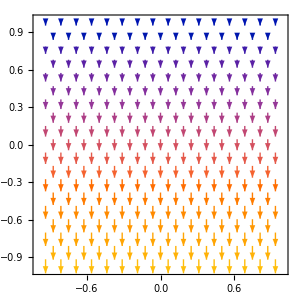
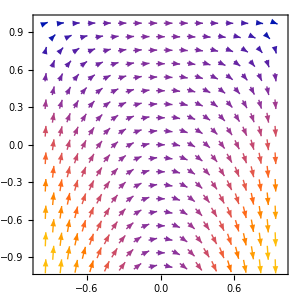
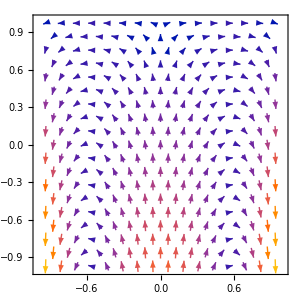
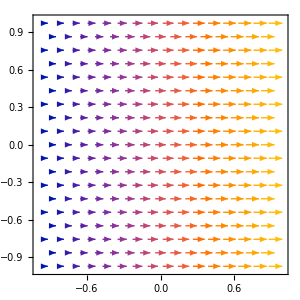
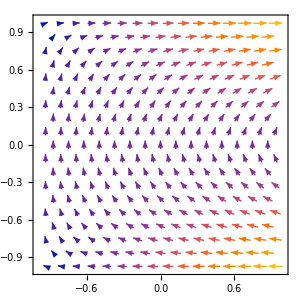
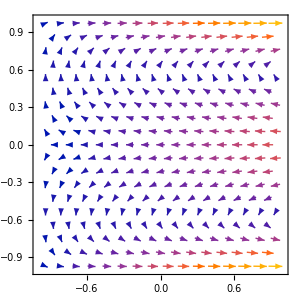
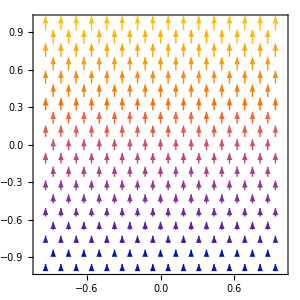
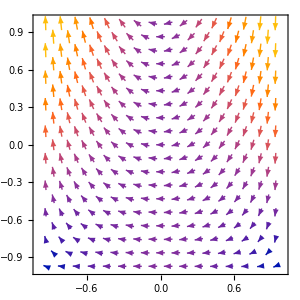

--- H1-Conforming Basis Functions ---

(1/4 (1-csi) (1-eta))

{{1,1}}

(1/4 (1+csi) (1-eta))

{{1,1}}

(1/4 (1+csi) (1+eta))

{{1,1}}

(1/4 (1-csi) (1+eta))

{{1,1}}

(1/2 (-1+csi) (1+csi) (-1+eta)
1/2 (-1+csi) csi (1+csi) (-1+eta))

{{2,1},{3,1}}

(-1/2 (1+csi) (-1+eta) (1+eta)
-1/2 (1+csi) (-1+eta) eta (1+eta))

{{1,2},{1,3}}

(-1/2 (-1+csi) (1+csi) (1+eta)
-1/2 (-1+csi) csi (1+csi) (1+eta))

{{2,1},{3,1}}

(1/2 (-1+csi) (-1+eta) (1+eta)
1/2 (-1+csi) (-1+eta) eta (1+eta))

{{1,2},{1,3}}

((-1+csi) (1+csi) (-1+eta) (1+eta)
(-1+csi) (1+csi) (-1+eta) eta (1+eta)
(-1+csi) csi (1+csi) (-1+eta) (1+eta)
(-1+csi) csi (1+csi) (-1+eta) eta (1+eta))

{{2,2},{2,3},{3,2},{3,3}}

--- Derivative H1-Conforming Basis Functions ---

(1/4 (-1+eta) | 1/4 (-1+csi)
(1-eta)/4 | 1/4 (-1-csi)
(1+eta)/4 | (1+csi)/4
1/4 (-1-eta) | (1-csi)/4
csi (-1+eta) | 1/2 (-1+csi) (1+csi)
1/2 (-1+3 csi^2) (-1+eta) | 1/2 (-1+csi) csi (1+csi)
-1/2 (-1+eta) (1+eta) | -((1+csi) eta)
-1/2 (-1+eta) eta (1+eta) | -1/2 (1+csi) (-1+3 eta^2)
-csi (1+eta) | -1/2 (-1+csi) (1+csi)
-1/2 (-1+3 csi^2) (1+eta) | -1/2 (-1+csi) csi (1+csi)
1/2 (-1+eta) (1+eta) | (-1+csi) eta
1/2 (-1+eta) eta (1+eta) | 1/2 (-1+csi) (-1+3 eta^2)
2 csi (-1+eta^2) | 2 (-1+csi^2) eta
2 csi eta (-1+eta^2) | (-1+csi^2) (-1+3 eta^2)
(-1+3 csi^2) (-1+eta^2) | 2 csi (-1+csi^2) eta
(-1+3 csi^2) eta (-1+eta^2) | csi (-1+csi^2) (-1+3 eta^2))

--- H(Ω, div) Basis Functions ---

(0 | -0.887298)

(0.2 | 1.3746
-0.154919 | -0.709839)

(0.112702 | 0)

(-0.174597 | 0.2
0.0901613 | -0.154919)

(0 | 0.112702)

--- Jacobian ---

(1/2 | 0
0 | 1/2)

--- Jacobian Determinant ---

1/4

--- Piola Transformation Te: Ω_ -> Ωhdiv ---

(0. | -1.7746
0.4 | 2.74919
-0.309839 | -1.41968
0.225403 | 0.
-0.349193 | 0.4
0.180323 | -0.309839
0. | 0.225403
-0.4 | 0.349193
0.309839 | -0.180323
-1.7746 | 0.
-2.74919 | -0.4
1.41968 | 0.309839
0.709839 | 0.
-0.549839 | 0.
0. | 0.0901613
0. | -0.0698387
-0.0901613 | 0.
0.0698387 | 0.
0.32 | 0.
-0.247871 | 0.
-1.23935 | 1.23935
0.64 | -0.96
0.96 | -0.64
-0.495742 | 0.495742)

```mathematica
CSI1 = ETA1 = -0.7745966692414834;
subst = {csi->CSI1,eta->ETA1};
n=2
{phivar, dphivar,orders} = H1Basis[n+1];
Table[Plot3D[phivar[[i,1]],{csi,-1,1},{eta,-1,1}],{i,9}]


phidiv = HDivOptimizedBasis[n]/.subst;
phidivgr = Flatten[HDivOptimizedBasis[n],1];

(*Setting a random element coordinate*)
X = {{0,0}, {1,0}, {1,1}, {0,1}};

(*Transforming master element into deformed element*)
{x, gradx} = Te[X, phivar, dphivar];

(*Calculating jacobian matrix and its determinant*)
{J, detJac} = Jacob[gradx];

(*Applying Piola transformation in Hdiv vector functions*)
phit = PiolaTransf[J, detJac, Flatten[phidiv,1]]/.subst

Table[VectorPlot[phidivgr[[i]],{csi,-1,1},{eta,-1,1},VectorScaling->Automatic, ImageSize->300], {i,12}]
PrintResults[phivar, orders, dphivar, phidiv, J, detJac, phit];
```

## Testing Optimized HDiv functions

## The div(Hdiv) functions can be represented by L2 functions

```mathematica
n=2
L2Funcs=H1Basis[n];
HDivFuncs=Flatten[HDivOptimizedBasis[n],1];
L2=L2Funcs[[1]]//Flatten;
div=Div[HDivFuncs,{csi,eta}]//Simplify
allfunc=Join[L2,div];
L2Mat=Parallelize[Table[Quiet[Integrate[allfunc[[i]]allfunc[[j]],{csi,-1,1},{eta,-1,1}]],{i,1,Length[allfunc]},{j,1,Length[allfunc]}]];
L2Mat//MatrixForm;
nL2=Length[L2];
Res=L2Mat[[nL2+1;;,nL2+1;;]]-L2Mat[[nL2+1;;,1;;nL2]].LinearSolve[L2Mat[[1;;nL2,1;;nL2]],L2Mat[[1;;nL2,nL2+1;;]]];
(*Chop[Res]//MatrixForm*)
Norm[Res]
```

## The rank of the div basis has be equal to the number of L2 functions

```mathematica
MatrixRank[L2Mat[[nL2+1;;,nL2+1;;]]]
Length[L2]
```

## All monomials whose divergence belongs to the L2 space need to be represented

```mathematica
AllPolx=Flatten[Table[{csi^i eta^j,0},{i,0,n+1},{j,0,n}],1];
AllPoly=Flatten[Table[{0,csi^i eta^j},{i,0,n},{j,0,n+1}],1];
AllPolxy=Join[AllPolx,AllPoly];
npoly=Length[AllPolxy]
nhdiv=Length[HDivFuncs]
allfunc=Join[AllPolxy,HDivFuncs];
L2Mat=Parallelize[Table[Quiet[Integrate[allfunc[[i]].allfunc[[j]],{csi,-1,1},{eta,-1,1}]],{i,1,Length[allfunc]},{j,1,Length[allfunc]}]];
L2Mat//MatrixForm;
nL2=Length[AllPolxy];
Res=L2Mat[[nL2+1;;,nL2+1;;]]-L2Mat[[nL2+1;;,1;;nL2]].LinearSolve[L2Mat[[1;;nL2,1;;nL2]],L2Mat[[1;;nL2,nL2+1;;]]];
(*Chop[Res]//MatrixForm*)
Norm[Res]
```

```mathematica
(*NotebookDelete[Cells[CellStyle->"Output"]];*)
```

## Function counting

## Hexahedra

### Number of L2 functions

```mathematica
nL2=(k+1)^3-1;
```

### Number of internal HDiv function by topology

edge functions (12 edges)

```mathematica
nEdge=k;
```

number of face functions (6 faces) in two directions for each face

```mathematica
nFace=k(k-1);
```

number of volume functions (3 directions)

```mathematica
nVolume=k(k-1)(k-1);
```

linear combination of the functions

```mathematica
nHdiv=a nEdge+b nFace+c nVolume
```

a k+b (-1+k) k+c (-1+k)^2 k

### Matching the function count

eliminating the highest order exponent

```mathematica
sol1=Solve[D[nL2,k,k,k]==D[nHdiv,k,k,k],c][[1]]
```

{c→1}

```mathematica
sol2=Solve[D[nL2- nVolume,k,k]==b D[nFace,k,k],b][[1]]
```

```mathematica
{b->5}
```

{b→5}

```mathematica
sol3=Solve[D[nL2-nVolume-5nFace,k]==a D[nEdge,k],a][[1]]
```

{a→7}

### Correspondence

```mathematica
nL2-nVolume-5 nFace-7 nEdge//Simplify
```

0

## Tetrahedra

### Number of L2 functions of order k

```mathematica
nL2=(k+3)(k+1)(k+2)/6-1;
```

### Number of internal HDiv function by topology

edge functions (6 edges)

```mathematica
nEdge=k;
```

number of face functions (4 faces) in two directions for each face

```mathematica
nFace=(k)(k-1)/2;
```

number of volume functions (3 directions)

```mathematica
nVolume=(k)(k-1)(k-2)/6;
```

linear combination of the functions

```mathematica
nHdiv=a nEdge+b nFace+c nVolume
```

a k+1/2 b (-1+k) k+1/6 c (-2+k) (-1+k) k

### Matching the function count

eliminating the highest order exponent

```mathematica
sol1=Solve[D[nL2,k,k,k]==D[nHdiv,k,k,k],c][[1]]
```

{c→1}

```mathematica
sol2=Solve[D[nL2- nVolume,k,k]==b D[nFace,k,k],b][[1]]
```

{b→3}

```mathematica
sol3=Solve[D[nL2-nVolume-3nFace,k]==a D[nEdge,k],a][[1]]
```

{a→3}

### Correspondence

```mathematica
nL2-nVolume-3 nFace-3 nEdge//Simplify
```

0

## Prism

### Number of L2 functions of order k

```mathematica
nL2=(k+1)(k+1)(k+2)/2-1;
```

### Number of internal HDiv function by topology

edge functions (6 edges)

```mathematica
nEdge=k;
```

2 triangular faces - 2 directions

```mathematica
nFace1=(k)(k-1)/2;
nFace1/.k->2
```

1

3 quadrilateral faces 2 directions

```mathematica
nFace2=(k)(k-1)/2;
nFace2/.k->2
```

1

number of volume functions vertical
number of bubble functions of order k horizontal times number of bubbles of order k+1 vertical

```mathematica
nVolume1=(k)(k-2)(k-1)/2;
```

number of volume functions horizontal
number of bubble functions of order k+1 horizontal times number of bubbles of order k vertical

```mathematica
nVolume2=(k-1)(k-1)(k)/2;
```

linear combination of the functions

```mathematica
nHdiv=a nEdge+b nFace1+c nVolume1+d nVolume2
```

a k+1/2 b (-1+k) k+1/2 c (-1+k)^2 k+1/2 d (-1+k)^2 k

### Matching the function count

eliminating the highest order exponent

```mathematica
sol1=Solve[D[nL2,k,k,k]==D[nHdiv,k,k,k],c][[1]]
```

{c→1-d}

```mathematica
sol2=Solve[D[nL2- nVolume1,k,k]==b D[nFace1,k,k],b][[1]]
```

{b→6}

```mathematica
sol3=Solve[D[nL2-nVolume1-6nFace1,k]==a D[nEdge,k],a][[1]]
```

{a→5}

### Correspondence

```mathematica
nL2-nVolume1-6 nFace1-5 nEdge//Simplify
```

0